## Preamble

### NOTE: Mathematica notebook default is not AutoSave!

Null

Null

```mathematica
Null
```

### Initialization

Follow the instructions on BB for installation and connecting to the Mathematica license server (note that you must be connected to NTNU’s IP domain (on campus or via VPN).

Load the StateDiagrams.m package (change the directory to the folder you are using) [provided by prof.em. Bjarne E. Helvik, NTNU]

```mathematica
(* Set the current directory to the directory/folder where you have stored the "StateDiagrams_mma-v12.m"-file *)
(* SetDirectory[$YOURDIRECTORY]*)
(** EXAMPLE ON POUL'S COMUPTER - you must change this **)
SetDirectory[$HomeDirectory];
SetDirectory["/Users/kajaprestneslind/Desktop/efefef/TTM4110/Labs/LAB IV"];
```

Import and list of the available functions in the package

```mathematica
Import["StateDiagrams_mma-v12.m"];
Names["Dependability`StateDiagrams`*"]
```

{ArrangeMatrix,DownTimeDensity,DownTimeDensityLaplace,GenHomogeneousSystem,KoutofN,KoutofNMode,KroenSum,LabelList,MDT,MergeStates,MTBF,MTFF,MTTF,MUT,ParallelMode,PlotDiagram,ProbStationary,ProbTransient,RelFunc,SeriesMode,SetDiagonal,StepPlot,UnAvailability}

### Warm up : Kroenker - example

#### Combine three 2-state Markov model into a 8-state model

```mathematica
(* Make 3 two state models with different λ and μ - repeat the above three times, or in a more compact way: *)
𝒬=Table[",",{2},{2}]; 
(𝒬[[1,2]]=Subscript[λ, #];𝒬[[2,1]]=Subscript[μ, #];Subscript[ℳ, #]= SetDiagonal[Transpose[𝒬]]) & /@ {1,2,3};
(Subscript[𝒲, #]={True,False}) & /@ {1,2,3};
(* Label the states with numbers *) 
(Subscript[ℒ, #]={1,0}) & /@ {1,2,3};
(* Combine the three models - using Kroenker-sum *)
Subscript[ℳ, T]=KroenSum[Subscript[ℳ, 1],Subscript[ℳ, 2],Subscript[ℳ, 3]];
Subscript[ℒ, T]=LabelList[Subscript[ℒ, 1],Subscript[ℒ, 2],Subscript[ℒ, 3]];
(* Define operational modes *) 
(* Series *) 
Subscript[𝒲, T] = SeriesMode[Subscript[𝒲, 1],Subscript[𝒲, 2],Subscript[𝒲, 3]];
(* Parallel *) 
Subscript[𝒲, T] = ParallelMode[Subscript[𝒲, 1],Subscript[𝒲, 2],Subscript[𝒲, 3]];
(* K-of-N *)
Subscript[𝒲, T] = KoutofNMode[Subscript[𝒲, 1],Subscript[𝒲, 2],Subscript[𝒲, 3],2];
(* Define you own - ex with Random *)
Subscript[𝒲, T]=Table[RandomChoice[{True,False}], {2^3}];
(* Define you own - ex when "Slow (S)" and "Agitated (A)" *)
Subscript[𝒲, T]= {True, True, True, True, True, True, False, False};
```

#### Plot the Markov model

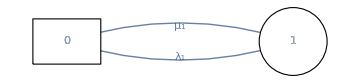
One model, ℳ_1 = -Graphics-

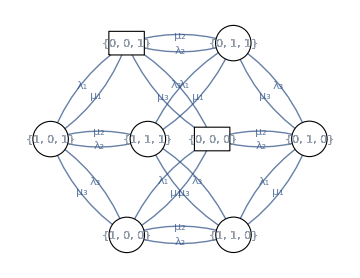
Three models combined, ℳ_T = -Graphics-

```mathematica
Print["One model, ℳ_1 = ",Show[PlotDiagram[Subscript[ℳ, 1],Subscript[𝒲, 1],Subscript[ℒ, 1]],ImageSize->Medium]];
Print["Three models combined, ℳ_T = ",Show[PlotDiagram[Subscript[ℳ, T],Subscript[𝒲, T],Subscript[ℒ, T]],ImageSize->Medium]];
```

Add transitions between states (0,0,1)→(1,1,1) [α_1] and (0,0,0)→(1,1,0) [α_2] in ℳ_T

```mathematica
(* Function that adds transitions with rate from state a->b in model M (state indexes in L) *) 
(* Transitions can be deleted by letting rate=0 *)
(* Note: M is transposed such that the cell (b,a) is from a to b *)
(* Note: SetDiagonal is needed to change the diagonal vector of M appropriatly *)
ChangeTransition[M_,L_,a_,b_,rate_]:= 
     Module[{tmp,idxa,idxb},
      idxa = Flatten[Position[#==a & /@ L, True]];
      idxb= Flatten[Position[#==b & /@ L , True]];
      tmp = M;
      tmp[[idxb,idxa]]=rate;
      SetDiagonal[tmp]
      ]
```

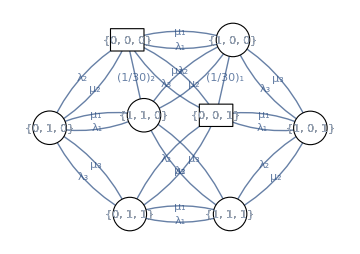
Model with two new transitions, ℳ_T = -Graphics-

```mathematica
Subscript[ℳ, T] = ChangeTransition[Subscript[ℳ, T],Subscript[ℒ, T],{0,0,1},{1,0,0},Subscript[α, 1]];
Subscript[ℳ, T] = ChangeTransition[Subscript[ℳ, T],Subscript[ℒ, T],{0,0,0},{1,1,0},Subscript[α, 2]];
Print["Model with two new transitions, ℳ_T = ",Show[PlotDiagram[Subscript[ℳ, T],Subscript[𝒲, T],Subscript[ℒ, T]],ImageSize->Medium]];
```

Remove transition between: {1,1,0}->{0,1,0} in ℳ_T, i.e., set rate to 0.

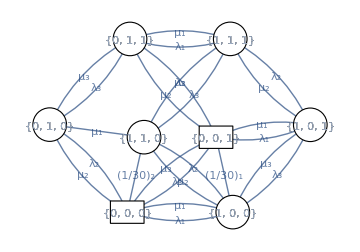
Model with one transition removed, ℳ_T = -Graphics-

```mathematica
Subscript[ℳ, T] = ChangeTransition[Subscript[ℳ, T],Subscript[ℒ, T],{1,1,0},{0,1,0},0];
Print["Model with one transition removed, ℳ_T = ",Show[PlotDiagram[Subscript[ℳ, T],Subscript[𝒲, T],Subscript[ℒ, T]],ImageSize->Medium]];
```

Obtain statistics from the model using a numerical set of parameters

```mathematica
(* Set parameters *)
𝒫 = Flatten[({Subscript[λ, #]->0.01/#,Subscript[μ, #]->1} )&/@{1,2,3}];
𝒫 = Flatten[AppendTo[𝒫,{Subscript[α, 1]->0.1,Subscript[α, 2]->0.5}]];
(* Obtain the steady state probabilties *)
ps =ProbStationary[Subscript[ℳ, T]/. 𝒫];
(* Obtain the transient state probabilties *)
(* Obtain the steady state UnAvailability *)
Print["UnAvailability, U = ",U=UnAvailability[ps,Subscript[𝒲, T]]];
Print["Availability, A = ",1-U];
(* Obtain the Mean UpTime *)
Print["Mean Up Time, MUT = ",MUT[Subscript[ℳ, T]/. 𝒫,Subscript[𝒲, T]]];
(* Obtain the Mean DownTime *)
Print["Mean Down Time, MDT = ",MDT[Subscript[ℳ, T]/. 𝒫,Subscript[𝒲, T]]];
```

UnAvailability, U = 0.0000468183

Availability, A = 0.999953

Mean Up Time, MUT = 10165.5

UnAvailability, U = 0.0000468183

Availability, A = 0.999953

Mean Up Time, MUT = 10165.5

Mean Down Time, MDT = 0.475956

Mean Down Time, MDT = 0.475956

## Lab IV: Transportation service dependability

CandID: 10031 
Worked with: 10033

### Task IV.A - Bus breakdowns

Each bus has a lot of mechanical and electromechanical parts, and firmware and software that need to be working so that the bus can drive. In this task, you are going to study the effect of mechanical failures (hardware) and software failures. All failure and repair times are negative exponentially distributed; 
- the time between hardware failures, T_h~n.e.d(λ_h) , 
- the time to hardware repair,  T_rh~n.e.d(μ_h),  
- the time between software failures, T_s~n.e.d(λ_s) , and 
- the time to software repair,  T_rs~n.e.d(μ_s).

#### Task IV.A.1

First, consider only hardware failures on a single bus.  The objective is to obtain the steady state probabilities that a bus is not working (the unavailability).  

a) Define the state variable and events, and draw the Markov model, ℳ_h.
b) What is the unavailability of the bus? Assume λ_h=1/14 [once every second week], and μ_h=1 [repair per day],  𝒫_h = {λ_h->1/14,μ_h->1}.
Then, assume that you have n=8 such busses, and with s=1,2,or 3 repairmen. At least 6 of the 8 busses need to be working in order to serve the passenger demand without too much delays.
c) Define the state variable and events, and draw the Markov model, ℳ_c.  What are working states in your model?
d) Use Mathematica to obtain the steady state probabilities. Use the parameter set  𝒫_h from above,  and change the number of repairmen, s=1,2,3.
e) What does mean time to first failure (MTFF) mean?  What is the MTFF of the bus (in model, ℳ_c)? (for s=1,2,3).
f)  What does mean time to failure (MTTF) mean? What is the MTTF of the bus (in model, ℳ_c)? (for s=1,2,3).
g)  What does mean down time (MDT) mean? What is the MDT of the bus (in model, ℳ_c)? (for s=1,2,3).
h) What is unavailability and the expected hours of downtime in a year the bus system (in model, ℳ_c) is unavailable? (for s=1,2,3).
i*) Discuss the different metrics from c) to g) with respect to how useful they are to express the importance of the number of repairmen.

a) In this simple scenario, we can define the state variables 0 and 1, where 0 represents an unavailable bus, and 1 represents an available bus. The events are defined by  and , where  is the rate of hardware failure, and   is the repair rate. Markov model is illustrated below.

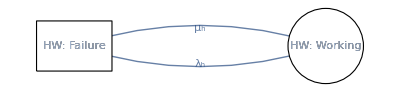

```mathematica
ClearAll[Q];
Q=Table[",",{2},{2}];
(Q[[1,2]]=Subscript[λ, h];
Q[[2,1]]=Subscript[μ, h]; Subscript[ℳ, h]=SetDiagonal[Transpose[Q]]);
(Subscript[𝒲, h]={True,False});
(Subscript[ℒ, h]={"HW: Working","HW: Failure"});
PlotDiagram[Subscript[ℳ, h],Subscript[𝒲, h],Subscript[ℒ, h]]
```

b) The probability expressions for a two state Markov model were derived in Lab III. Hence, we have that  is given by:

```mathematica
Subscript[𝒫, h] = {Subscript[λ, h] -> 1/14, Subscript[μ, h] -> 1};
p_unavailable = Subscript[λ, h]/(Subscript[λ, h]+Subscript[μ, h])/. Subscript[𝒫, h]
```

1/15

The probability  is calculated to be  0.0667, which means that a bus is unavailable 6.67% of the time. 
We can also check this using Mathematica features

```mathematica
ps = ProbStationary[Subscript[ℳ, h] /. Subscript[𝒫, h] ];
Print["Unavailability, U = ", U = UnAvailability[ps, Subscript[𝒲, h]]]
```

Unavailability, U = 1/15

c) In this model we have one state variable describing how many of the buses are operational. The events are defined by  and , where  is the rate of hardware failure, and   is the repair rate. Since is the rate per bus, the rate is dependent of number of operational buses. Even though the system will work up until there is no operational buses, I have chosen to define the working states to only be then we have 6 or more working buses, because that is what we want in order to serve the demand without too much delays

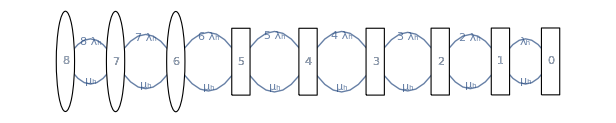

```mathematica
ClearAll[Q];

Q=Table[0,{9},{9}];
For[k=1,k<=8,k++,
Q[[k,k+1]]=Subscript[μ, h];
Q[[k+1,k]]=k*Subscript[λ, h]; 
];

Subscript[ℳ, c] = SetDiagonal[Transpose[Q ]];
Subscript[𝒲, c]={False,False,False,False,False,False,True,True,True};
Subscript[ℒ, c]=Range[0,8];

PlotDiagram[Subscript[ℳ, c],Subscript[𝒲, c],Subscript[ℒ, c]]
```

d) The steady state probabilities show how the number of repairmen affects the system, by influencing the likelihood of having more operational buses. With one repairman, , the system often has 8 operating buses, but there is still a chance of having less than 8,  and in our case - less than 6. When adding a second repairman, , this instantly increases the probability for the higher operational states. We can also see that adding a third repairman, has a rather small impact on the system, which indicates that  makes the ideal number of repairmen. Index one in the list shows the state probability for one operational bus, etc.

```mathematica
ClearAll[Q,s];

Q=Table[0,{9},{9}];
For[k=1,k<=8,k++,
Q[[k,k+1]]=Subscript[μ, h];
Q[[k+1,k]]=k*Subscript[λ, h]; 
];
Q[[8,9]] = Min[1, Subscript[μ, h]];
Q[[7,8]] = Min[2, Subscript[μ, h]];

Subscript[ℳ, c] = SetDiagonal[Transpose[Q ]];
Subscript[𝒲, c]={False,False,False,False,False,False,True,True,True};

results = {};
Do[
ps = ProbStationary[Subscript[ℳ, c] /.{Subscript[λ, h] -> (Subscript[λ, h]/. Subscript[𝒫, h]), Subscript[μ, h] -> ( Subscript[μ, h]/. Subscript[𝒫, h]) *s} ]//N;
AppendTo[results, ps];
Print["Steady state probabilities for s = ", s, ": ", ps] , {s, 1, 3}
]
```

Steady state probabilities for s = 1: {0.0000133998,0.000187598,0.00131318,0.00612819,0.0214487,0.0600562,0.140131,0.280262,0.490459}

Steady state probabilities for s = 2: {1.21883×10^-7,3.41271×10^-6,0.000047778,0.000445928,0.0031215,0.0174804,0.0815751,0.3263,0.571026}

Steady state probabilities for s = 3: {1.07856×10^-8,4.52997×10^-7,9.51293×10^-6,0.000133181,0.0013984,0.0117466,0.082226,0.328904,0.575582}

e) Mean time to first failure is the average time of functionality before a failure impacts the product/system for the first time.

```mathematica
Do[Print["MTFF for s = ", s, ": ", MTFF[Subscript[ℳ, c] /.{Subscript[λ, h] -> (Subscript[λ, h]/. Subscript[𝒫, h]), Subscript[μ, h] -> ( Subscript[μ, h]/. Subscript[𝒫, h]) *s}, Reverse[Subscript[𝒲, c]]]//N], {s, 1, 3}]
```

MTFF for s = 1: 3.22449

MTFF for s = 2: 1.55485

MTFF for s = 3: 1.02419

f) Mean time to failure is the average time a product/system operates before a failure a occurs.

```mathematica
Do[Print["MTTF for s = ", s, ": ", MTTF[Subscript[ℳ, c] /.{Subscript[λ, h] -> (Subscript[λ, h]/. Subscript[𝒫, h]), Subscript[μ, h] -> ( Subscript[μ, h]/. Subscript[𝒫, h]) *s}, Subscript[𝒲, c] ]//N], {s, 1, 3}]
```

MTTF for s = 1: 20.7628

MTTF for s = 2: 34.0625

MTTF for s = 3: 34.0625

g) Mean down time is a measure for the average time a product/system is down after failure while it is being repaired and maintained. In other words,  the average time it is non-operational.

```mathematica
Do[Print["MDT for s = ", s, ": ", MDT[Subscript[ℳ, c] /.{Subscript[λ, h] -> (Subscript[λ, h]/. Subscript[𝒫, h]), Subscript[μ, h] -> ( Subscript[μ, h]/. Subscript[𝒫, h]) *s}, Subscript[𝒲, c] ]//N], {s, 1, 3}]
```

MDT for s = 1: 1.4844

MDT for s = 2: 0.603509

MDT for s = 3: 0.377078

h) Unavailability measures the proportion of time that a system is non-operational. We can use this proportion to calculate the total of downtime in our system, in this case, on an annual basis.

```mathematica
unavailabilities = {};
 
Do[
unavailable = UnAvailability[results[[s]], Subscript[𝒲, c] ]//N;
AppendTo[unavailabilities, unavailable];
Print["Unavailablity for s = ", s, ": ", unavailabilities[[s]]], {s, 1, 3}
]

hoursYear = 365 * 24; 

Do[
Print["Expected hours of downtime per year for s = ", s, ": ", unavailabilities[[s]] * hoursYear], {s, 1, 3}
]
```

Unavailablity for s = 1: 0.0891472

Unavailablity for s = 2: 0.0210991

Unavailablity for s = 3: 0.0132881

Expected hours of downtime per year for s = 1: 780.93

Expected hours of downtime per year for s = 2: 184.828

Expected hours of downtime per year for s = 3: 116.404

i) After analyzing the different metrics, we observe that they all improve as the number of repairmen increase, with the most significant improvement occurring when the number of repairmen increase from one to two. This change leads to a significant reduction in downtime and enhances system availability.  Adding a third repairman continues to improve the metrics, even though the improvement of the metrics are remarkably smaller, indicating that this addition is rather unnecessary.

#### Task IV.A.2

Now, consider only software failures. There are no constraints regarding repairmen because it is assumed that the software failures are repaired by rebooting the software on the bus (at an end station).

Two types of software failures are included:
1. Omission failures : the failure is detected and the bus has to return to the depot and be diagnosed and restarted (autonomous process), with failure rate T_o~n.e.d(λ_o) and repair rate T_ro~n.e.d(μ_o). The bus cannot serve any passengers in this state.
2. Value failures : the information sent and received is valid but wrong (undetected), with failure rate T_v~n.e.d(λ_v). Value failures are not detected and repaired and will be in the system until you reboot the bus. A reboot is only done after an omission failure has been detected.  The omission failure rate after a value failure is doubled, i.e., 2 λ_o.  The bus is not able to select the  best route and therefor only 60% of the passengers are served (within acceptable waiting time). 

a) Define the state variable and events, and draw the Markov model.
b) Use Mathematica to obtain the steady state probabilities. Assume λ_o=1/2 [once every second day], and μ_o=8 [repairs per day], and  λ_v=1/4 [once every forth day], 𝒫_s = {λ_o->1/2,μ_o->8,λ_v->1/4}. 
c) Define the down states in this model and obtain the availability.
d) What is the average % of passengers the bus can handle?  Discuss this relative to availability.

a) I have defined one state variable, that can take one of three different values: {“Working”, “Omission”, and “Value”}.  The event are defined by λ_o, λ_v, and μ_o, where  λ_o represents the rate of omission failure,  λ_v represents the rate of value failure, and μ_o represents the repair rate after omission failure.

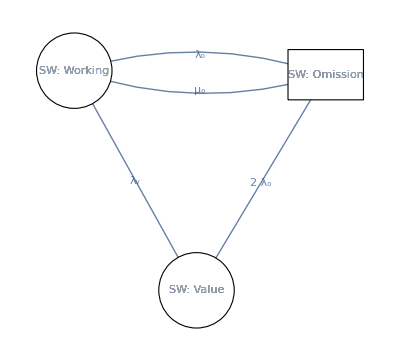

```mathematica
ClearAll[Q]
Q = Table[0, {3}, {3}];
Q[[1, 2]] = Subscript[λ, o];
Q[[2, 1]] = Subscript[μ, o];
Q[[1, 3]] = Subscript[λ, v];
Q[[3, 2]] = 2*Subscript[λ, o];

Subscript[ℳ, s] = SetDiagonal[Transpose[Q ]];
Subscript[𝒲, s]={True,False, True};
Subscript[ℒ, s]={"SW: Working", "SW: Omission", "SW: Value"};

PlotDiagram[Subscript[ℳ, s],Subscript[𝒲, s],Subscript[ℒ, s]]
```

b) The steady state probabilities of the system is calculated below.

```mathematica
Subscript[𝒫, s] = {Subscript[λ, o]->1/2,Subscript[μ, o]->8,Subscript[λ, v]->1/4};
ps = ProbStationary[Subscript[ℳ, s] /. Subscript[𝒫, s]]//N;
Print["Steady state probabilities: ", ps]
```

Steady state probabilities: {0.744186,0.0697674,0.186047}

c) The only down state in this model is when a omission failure occurs. The availability will be the amount of time the bus is not in this down state.

```mathematica
sAvailability = 1 - UnAvailability[ps, Subscript[𝒲, s]];
Print["The availability of the bus is ", sAvailability]
```

The availability of the bus is 0.930233

d) When a value fail has occurred the bus will still be available, but a consequence of this error is that the bus is not able to select the best route and only serves 60% of the passengers. Because of this, I have calculated the average passenger handling with respect to this limitation.

```mathematica
sAverage = ps[[1]] +  ps[[2]]*0.6;
Print["On average, the bus can handle ", sAverage*100, "% of passengers."]
```

On average, the bus can handle 78.6047% of passengers.

#### Task IV.A.3*

A bus can only drive if both the hardware and the software of the bus is working. The objective is still to obtain the steady state probability of the number of failed busses in the system.  

a) Combine the models  ℳ_h and ℳ_s from above into a new model ℳ_c [use Köeneker-sum]. Plot the diagram of ℳ_c.
b) Obtain the availability and average number of passengers handled by a bus. 
The bus that gets a mechanical failure will be returned to the garage for repair.  Any software failure (omission or value) will also be removed when the bus is repaired. 
c) Modify the transitions in model ℳ_c to include the fact that software failures are also removed after a repair. Show this on paper.
d) Implement the changes ℳ_c by use of the ChangeTransition[] function provided below.  Call this new model ℳ_x, and plot the diagram of ℳ_x. 
e) Obtain the availability and average number of passengers handled by a bus in model ℳ_x and compare it with the values from IV.A.3.b) for ℳ_c.  Based on this, would you say that the ℳ_c is a good approximation of ℳ_x?
In principle, you can combine the bus model to form a fleet of busses (e.g., 8 as above). 
f) If you have 8 busses, and each bus is modelled by ℳ_c (or ℳ_x): how many states will you have when you combine the models by Kronecker sum?  
g) Combine 2 (only!) busses into a model ℳ_t, and plot the diagram for this model, use KroenSum[] again. Comment on how useful this model is? ( how readable it is, what metrics can you obtain).  How many states do you have in the model?
h) To make the model more scalable, how can you model and obtain the (un)availability if you ignore the fact that you have a limited number of repairmen.  Assume that both busses needs to be operational (“Up”) in order for the bus system to be in operation (the system is “Up”). Compare the system unavailability from the combined model ℳ_t with the alternative approach you suggest.

Module for adding and deleting transitions in ℳ_T

```mathematica
(* Function that adds transitions with rate from state a->b in model M (state indexes in L) *) 
(* Transitions can be deleted by letting rate=0 *)
(* Note: M is transposed such that the cell (b,a) is from a to b *)
(* Note: SetDiagonal is needed to change the diagonal vector of M appropriatly *)
ChangeTransition[M_,L_,a_,b_,rate_]:= 
     Module[{tmp,idxa,idxb},
      idxa = Flatten[Position[#==a & /@ L, True]];
      idxb= Flatten[Position[#==b & /@ L , True]];
      tmp = M;
      tmp[[idxb,idxa]]=rate;
      SetDiagonal[tmp]
      ]
```

a) Using the Köeneker-sum, ℳ_c has been plotted below. We can see that we have a new diagram combining all states from our previous models  ℳ_h and ℳ_s.

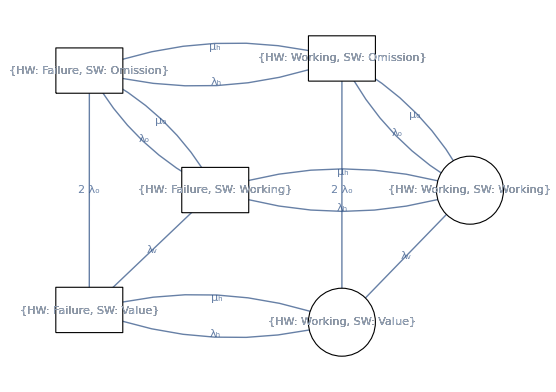

```mathematica
Subscript[ℳ, c]=KroenSum[Subscript[ℳ, h],Subscript[ℳ, s]];
Subscript[ℒ, c]=LabelList[Subscript[ℒ, h],Subscript[ℒ, s]];
Subscript[𝒲, c] = SeriesMode[Subscript[𝒲, h],Subscript[𝒲, s]];
PlotDiagram[Subscript[ℳ, c],Subscript[𝒲, c],Subscript[ℒ, c]]
```

b)  Since we have no way to calculate the number of passengers, the percentage of passenger handling is calculated instead. This is done in the same way as in IV.A.2.

```mathematica
Clear[ps] 
ps = ProbStationary[Subscript[ℳ, c] /. Subscript[𝒫, s]  /. Subscript[𝒫, h]  ]//N;
Print["Steady state probabilities: ", ps]
cAvailability = 1 - UnAvailability[ps, Subscript[𝒲, c]];
Print["The availability of the bus is ", cAvailability]
cAverage = ps[[1]] +  ps[[3]]*0.6;
Print["On average, the bus can handle ", cAverage*100, "% of the passengers."]
```

Steady state probabilities: {0.694574,0.0651163,0.173643,0.0496124,0.00465116,0.0124031}

The availability of the bus is 0.868217

On average, the bus can handle 79.876% of the passengers.

c) The new Markov model is illustrated below. The grey transitions are the ones we wanted to remove, and the green represents the new transitions. 

-Graphics-


d) Using ChangeTransition to add and remove transitions. New model is plotted below.

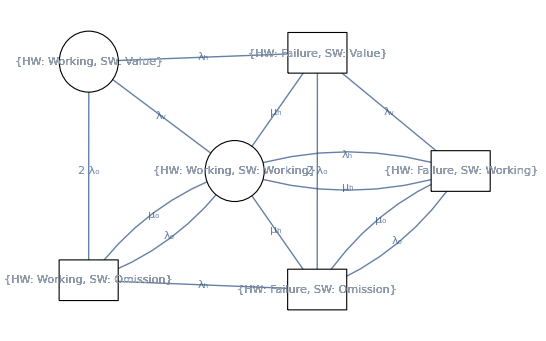

```mathematica
Subscript[ℳ, x]=Subscript[ℳ, c];
Subscript[ℒ, x]=Subscript[ℒ, c];
Subscript[𝒲, x]=Subscript[𝒲, c];

(*Removing the grey transitions*)
Subscript[ℳ, x] = ChangeTransition[Subscript[ℳ, x],Subscript[ℒ, x],{"HW: Failure","SW: Omission"},{"HW: Working","SW: Omission"} ,0];
Subscript[ℳ, x] = ChangeTransition[Subscript[ℳ, x],Subscript[ℒ, x],{"HW: Failure","SW: Value"},{"HW: Working","SW: Value"} ,0];

(*Adding the green transitions*)
Subscript[ℳ, x] = ChangeTransition[Subscript[ℳ, x],Subscript[ℒ, x],{"HW: Failure","SW: Omission"},{"HW: Working","SW: Working"} ,Subscript[μ, h]];
Subscript[ℳ, x] = ChangeTransition[Subscript[ℳ, x],Subscript[ℒ, x],{"HW: Failure","SW: Value"},{"HW: Working","SW: Working"} ,Subscript[μ, h]];

PlotDiagram[Subscript[ℳ, x],Subscript[𝒲, x],Subscript[ℒ, x]]
```

e) Since all of the measurements are nearly identical for the two models, we can say that ℳ_c is a good approximation of ℳ_x.

```mathematica
Subscript[𝒫, x] = {Subscript[λ, h]->1/14,Subscript[μ, h]->1,Subscript[λ, o]->1/2,Subscript[μ, o]->8,Subscript[λ, v]->1/4};
ps = ProbStationary[Subscript[ℳ, x] /. Subscript[𝒫, x]]//N;
Print["Steady state probabilities: ", ps]
xAvailability = 1 - UnAvailability[ps, Subscript[𝒲, x]];
Print["The availability of the bus is ", xAvailability]
xAverage = ps[[1]] +  ps[[3]]*0.6;
Print["On average, the bus can handle ", xAverage*100, "% of the passengers."]
```

Steady state probabilities: {0.704834,0.064038,0.164461,0.0499246,0.00462785,0.0121142}

The availability of the bus is 0.869295

On average, the bus can handle 80.3511% of the passengers.

f) When each bus has 6 states, you will get  states when you combine  buses. If  , we have =1 679 616  states in total. 

g) This model has = 36 states. As you can see, the model is very hard to read and not very helpful. I could have changed the labels somehow, but I think that would have made a small difference to the model overall. Using Mathematica , we can obtain the same metrics as before, but it is very hard to get any information out of the model itself.

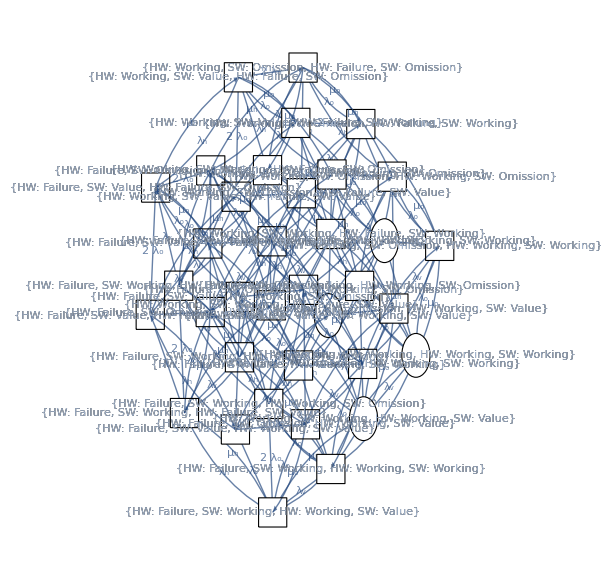

```mathematica
Subscript[ℳ, t]=KroenSum[Subscript[ℳ, h],Subscript[ℳ, s], Subscript[ℳ, h],Subscript[ℳ, s]];
Subscript[ℒ, t]=LabelList[Subscript[ℒ, h],Subscript[ℒ, s], Subscript[ℒ, h],Subscript[ℒ, s]];
Subscript[𝒲, t] = SeriesMode[Subscript[𝒲, h],Subscript[𝒲, s], Subscript[𝒲, h],Subscript[𝒲, s]];
PlotDiagram[Subscript[ℳ, t],Subscript[𝒲, t],Subscript[ℒ, t]]
```

h) My suggestion for an alternative approach to calculate the availability of several buses is the following:

```mathematica
ps = ProbStationary[Subscript[ℳ, t] /. Subscript[𝒫, x]]//N;
Print["The unavailability of the buses in the extended model is: ", 1 - UnAvailability[ps, Subscript[𝒲, t]]]
Print["The unavailabilty of one bus combineds as if there were two: ", cAvailability^2 ]
```

The unavailability of the buses in the extended model is: 0.753801

The unavailabilty of one bus combineds as if there were two: 0.753801

The unavailabilty of one bus combineds as if there were two: 0.753801

The first method uses a the model to determine availability, while the second method assumes the buses operate independently, allowing us to approximate the availability by squaring the availability of a single bus. This second method is simpler, faster, and gives, in this case, the exact same result as the complex model, making it a more practical alternative. When we have a large amount of buses, the number of states to investigate will get very big. Therefore, combining the results for one bus gives a simpler calculation, but still a reasonable value.

### Task IV.B - Road blocks after severe weather

In this task you are going to study the effect of severe weather that leads to road blocks.  Assume now that the busses can take any of the available routes (no preplanned routes as in Lab III). The time between severe weather is T_wo and it last T_wl. Both are n.e.d., i.e., T_wo~n.e.d(α)  and   T_wl~n.e.d(β).  Numerical values are:  𝒫_r={α->1/30,β->1/2} [unit is 1/day].

a) What is the availability and reliability of road i if the weather “hits” this road with the probability p_i? (Symbolic expressions expected)
b) What is the availability and reliability after t=100 days of the different roads if the weather “hits” a road i with the probabilities  
𝒫_a={p_1→0.0714,p_2→0.0714,p_3→0.0714,p_4→0.1,p_5→0.0714,p_6→0.1,p_7→0.1,p_8→0.0483,p_9→0.0483,p_10→0.0483,p_11→0.0483,p_12→0.0714,p_13→0.0714,p_14→0,p_15→0.0714}
c) Which assumptions do you have to make in order to use Reliability Block Diagram (RBD)?
d) Assume that road R_14 in the system description is under maintenance and therefor always blocked. Make Reliability Block Diagram (RBD) for  the following end stop combinations [one for each]
	- ℳ_RBD1, the bus routes between ES_1->ES_3(only eastbound)
	- ℳ_RBD2, the bus routes between ES_1->ES_4(only eastbound)
	- ℳ_RBD3, the bus routes between ES_2->ES_3(only eastbound)
	- ℳ_RBD4, the bus routes between ES_2->ES_4(only eastbound)
e) Use your models to obtain the availability (both symbolically and numerically) of the four alternative end stop, ES_i combinations.  Which of the four has highest availability?  What is the probability that bus stop 5 cannot be served (is unavailable)?
f) Obtain the reliability function, R_13(t), of  ES_1->ES_3. Plot the function with parameters in 𝒫_r and  𝒫_a. What is the probability that the bus service between ES_1->ES_3 works without interruptions for 10 days?
g*) Assume that R_13 is never blocked by sever weather. What is the most dominant/likely (combination of) roads wrt. probability of the routes between  ES_1->ES_3?  [hint: define (minimum) cut sets].

a) The availability for the weather to hit the road is given by 
	𝒜

     In our case, the road is split into several roads. This gives the availability of road  as 
     	𝒜
     	     
     The reliability of road  at time  is given by 
     	ℛ

```mathematica
roadAvailability[p_]:=β/(p*α+β);
roadReliability[t_,p_]:=Exp[-p*α*t];
```

b) The availability and  reliability after t = 100 days of the different roads are represented in the table below.

```mathematica
α = 1/30;
β = 1/2;
Subscript[𝒫, a]={0.0714,0.0714,0.0714,0.1,0.0714,0.1,0.1,0.0483,0.0483,0.0483,0.0483,0.0714,0.0714,0,0.0714};

𝒜 = {Subscript[𝒶, 1] ->roadAvailability[Subscript[𝒫, a][[1]]], Subscript[𝒶, 2] ->roadAvailability[Subscript[𝒫, a][[2]]], 
Subscript[𝒶, 3] ->roadAvailability[Subscript[𝒫, a][[3]]], Subscript[𝒶, 4] ->roadAvailability[Subscript[𝒫, a][[4]]], 
Subscript[𝒶, 5] ->roadAvailability[Subscript[𝒫, a][[5]]], Subscript[𝒶, 6] ->roadAvailability[Subscript[𝒫, a][[6]]], 
Subscript[𝒶, 7] ->roadAvailability[Subscript[𝒫, a][[7]]], Subscript[𝒶, 8] ->roadAvailability[Subscript[𝒫, a][[8]]], 
Subscript[𝒶, 9] ->roadAvailability[Subscript[𝒫, a][[9]]], Subscript[𝒶, 10] ->roadAvailability[Subscript[𝒫, a][[10]]],
Subscript[𝒶, 11] ->roadAvailability[Subscript[𝒫, a][[11]]], Subscript[𝒶, 12] ->roadAvailability[Subscript[𝒫, a][[12]]], 
Subscript[𝒶, 13] ->roadAvailability[Subscript[𝒫, a][[13]]], Subscript[𝒶, 14] ->roadAvailability[Subscript[𝒫, a][[14]]], 
Subscript[𝒶, 15] ->roadAvailability[Subscript[𝒫, a][[15]]]};

ℛ[t_] = {Subscript[𝓇, 1]-> roadReliability[t,Subscript[𝒫, a][[1]]], Subscript[𝓇, 2]->roadReliability[t,Subscript[𝒫, a][[2]]],
 Subscript[𝓇, 3]-> roadReliability[t,Subscript[𝒫, a][[3]]], Subscript[𝓇, 4]-> roadReliability[t,Subscript[𝒫, a][[4]]],
 Subscript[𝓇, 5]-> roadReliability[t,Subscript[𝒫, a][[5]]], Subscript[𝓇, 6]-> roadReliability[t,Subscript[𝒫, a][[6]]],
Subscript[𝓇, 7]-> roadReliability[t,Subscript[𝒫, a][[7]]], Subscript[𝓇, 8]-> roadReliability[t,Subscript[𝒫, a][[8]]],
Subscript[𝓇, 9]->roadReliability[t,Subscript[𝒫, a][[9]]], Subscript[𝓇, 10]-> roadReliability[t,Subscript[𝒫, a][[10]]], 
Subscript[𝓇, 11]-> roadReliability[t,Subscript[𝒫, a][[11]]], Subscript[𝓇, 12]-> roadReliability[t,Subscript[𝒫, a][[12]]], 
Subscript[𝓇, 13]-> roadReliability[t,Subscript[𝒫, a][[13]]], Subscript[𝓇, 14]->roadReliability[t,Subscript[𝒫, a][[14]]],  
Subscript[𝓇, 15]-> roadReliability[t,Subscript[𝒫, a][[15]]]};

Subscript[ℛ, 100] = Block[{t=100},ℛ[t]];

results=TableForm[
Transpose[{Subscript[𝒫, a],𝒜,Subscript[ℛ, 100]}],
TableHeadings->{None,{"Probability","Availability","Reliability after 100 days"}}];
results
```

Probability | Availability | Reliability after 100 days
0.0714 | 𝒶_1→0.995263 | 𝓇_1→0.788203
0.0714 | 𝒶_2→0.995263 | 𝓇_2→0.788203
0.0714 | 𝒶_3→0.995263 | 𝓇_3→0.788203
0.1 | 𝒶_4→0.993377 | 𝓇_4→0.716531
0.0714 | 𝒶_5→0.995263 | 𝓇_5→0.788203
0.1 | 𝒶_6→0.993377 | 𝓇_6→0.716531
0.1 | 𝒶_7→0.993377 | 𝓇_7→0.716531
0.0483 | 𝒶_8→0.99679 | 𝓇_8→0.851292
0.0483 | 𝒶_9→0.99679 | 𝓇_9→0.851292
0.0483 | 𝒶_10→0.99679 | 𝓇_10→0.851292
0.0483 | 𝒶_11→0.99679 | 𝓇_11→0.851292
0.0714 | 𝒶_12→0.995263 | 𝓇_12→0.788203
0.0714 | 𝒶_13→0.995263 | 𝓇_13→0.788203
0 | 𝒶_14→1 | 𝓇_14→1
0.0714 | 𝒶_15→0.995263 | 𝓇_15→0.788203

c) In order to make a Reliability Block Diagram we need to assume the following: 
	- All systems fail independent of other subsystems, given that the system consists of more than one subsystem.
	- All systems are restored independent of the other subsystems, after failure
	- The system works as it is supposed to regarding repairs and 

d) 
	- ℳ_RBD1, the bus routes between ES_1->ES_3(only eastbound)
-Graphics-
	
	- ℳ_RBD2, the bus routes between ES_1->ES_4(only eastbound)
-Graphics-
	
	- ℳ_RBD3, the bus routes between ES_2->ES_3(only eastbound)
-Graphics-
	
	- ℳ_RBD4, the bus routes between ES_2->ES_4(only eastbound)
-Graphics-

e) The availability of a system in series is given  by 
	𝒜
     
     and in parallel
	𝒜
     	
    The formulas for our end stop combinations are derived from the equations above. They can be observed below.

```mathematica
(*Availability from end stop to end stop*)
Subscript[𝒜, RBD1]=(1-(1-(Subscript[𝒶, 1]*Subscript[𝒶, 5]*Subscript[𝒶, 8]))*(1-(Subscript[𝒶, 2]*Subscript[𝒶, 7]*Subscript[𝒶, 9])))*Subscript[𝒶, 13];
Subscript[𝒜, RBD2]=(1-(1-(Subscript[𝒶, 1]*Subscript[𝒶, 5]*Subscript[𝒶, 10]))*(1-(Subscript[𝒶, 2]*Subscript[𝒶, 7]*Subscript[𝒶, 11])))*Subscript[𝒶, 15];
Subscript[𝒜, RBD3]=(1-(1-(Subscript[𝒶, 3]*Subscript[𝒶, 7]*Subscript[𝒶, 9]))*(1-(Subscript[𝒶, 4]*Subscript[𝒶, 6]*Subscript[𝒶, 8])))*Subscript[𝒶, 13];
Subscript[𝒜, RBD4]=(1-(1-Subscript[𝒶, 3]*Subscript[𝒶, 7]*Subscript[𝒶, 11])*(1-Subscript[𝒶, 4](1-(1-Subscript[𝒶, 6]*Subscript[𝒶, 10])(1-Subscript[𝒶, 12]))))*Subscript[𝒶, 15];

Print["ES_1->ES_3: Availability 𝒜 = ",Subscript[𝒜, RBD1], " = ", Subscript[𝒜, RBD1]/.𝒜]
Print["ES_1->ES_4: Availability 𝒜 = ",Subscript[𝒜, RBD2], " = ", Subscript[𝒜, RBD2]/.𝒜]
Print["ES_2->ES_3: Availability 𝒜 = ",Subscript[𝒜, RBD3], " = ", Subscript[𝒜, RBD3]/.𝒜]
Print["ES_2->ES_4: Availability 𝒜 = ",Subscript[𝒜, RBD4], " = ", Subscript[𝒜, RBD4]/.𝒜]
```

ES_1->ES_3: Availability 𝒜 = (1-(1-𝒶_1 𝒶_5 𝒶_8) (1-𝒶_2 𝒶_7 𝒶_9)) 𝒶_13 = 0.99508

ES_1->ES_4: Availability 𝒜 = (1-(1-𝒶_1 𝒶_5 𝒶_10) (1-𝒶_2 𝒶_7 𝒶_11)) 𝒶_15 = 0.99508

ES_2->ES_3: Availability 𝒜 = (1-(1-𝒶_4 𝒶_6 𝒶_8) (1-𝒶_3 𝒶_7 𝒶_9)) 𝒶_13 = 0.995026

ES_2->ES_4: Availability 𝒜 = (1-(1-𝒶_3 𝒶_7 𝒶_11) (1-𝒶_4 (1-(1-𝒶_6 𝒶_10) (1-𝒶_12)))) 𝒶_15 = 0.995166

We can see that ES_2->ES_4 has the highest availability,  although the margin is quite small.

When calculating the probability that bus stop 5 is unavailable, we need to check the probability that , or  and are unavailable, as those roads are the ones leading to . Making an expression for 𝒮_5 unavailability using the inclusion-exclusion principle:

```mathematica
Subscript[unavail𝓇, 2]=1 -Subscript[𝒶, 2] /.𝒜;
Subscript[unavail𝓇, 3]=1 -Subscript[𝒶, 3] /.𝒜;
Subscript[unavail𝓇, 7]=1 -Subscript[𝒶, 7] /.𝒜;

Subscript[unavail𝒮, 5]= Subscript[unavail𝓇, 7] + Subscript[unavail𝓇, 2]*Subscript[unavail𝓇, 3] - Subscript[unavail𝓇, 7]* Subscript[unavail𝓇, 2] * Subscript[unavail𝓇, 3];
Print["The probability of stop  being unavailable is ", Subscript[unavail𝒮, 5]"."]
```

The probability of stop  being unavailable is 0.00664481 .

f) The reliability of a system in series is given by
     	ℛ

     and in parallel
     	ℛ
     
     Thus, we get that the reliability function for ES_1->ES_3 is 
     	ℛ_13 (t) = (1 - (1 - (𝓇_1(t)  𝓇_5(t)  𝓇_8 (t)))(1 - (𝓇_2(t)  𝓇_7(t)  𝓇_9 (t)))) 𝓇_13 (t)
     	ℛ_13(t)=(1-(1-(𝓇_1(t)*𝓇_5(t)*𝓇_8(t)))*(1-(𝓇_2(t)*𝓇_7(t)*𝓇_9(t)))*𝓇_13(t)

The probability that the bus service between  works without interruptions for 10 days is 0.972226.

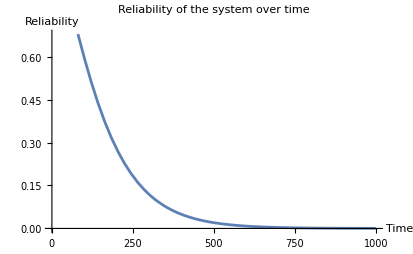

```mathematica
Subscript[ℛ, 10days]= (1-(1-(Subscript[𝓇, 1]*Subscript[𝓇, 5]*Subscript[𝓇, 8]))*(1-(Subscript[𝓇, 2]*Subscript[𝓇, 7]*Subscript[𝓇, 9])))*Subscript[𝓇, 13]  /.ℛ[10];
Print["The probability that the bus service between  works without interruptions for 10 days is ", Subscript[ℛ, 10days],"."]

Subscript[ℛ, 13]=(1-(1-(Subscript[𝓇, 1]*Subscript[𝓇, 5]*Subscript[𝓇, 8]))*(1-(Subscript[𝓇, 2]*Subscript[𝓇, 7]*Subscript[𝓇, 9])))*Subscript[𝓇, 13] ;

Plot[Subscript[ℛ, 13] /. ℛ[t], {t, 0, 1000}, AxesLabel->{"Time","Reliability"}, PlotLabel->"Reliability of the system over time" ]
```

Here we can see that the reliability function behaves as a n.e.d for big values of t.

g) To make our calculations simpler, we define cut sets  to identify the minimal combinations of component failures that will lead to a system failure. The minimal cut sets of ES_1->ES_3 are:
	set_1 = {R_1, R_2}
	set_2 = {R_1, R_7}
	set_3 = {R_1, R_9}
	set_4 ={R_5, R_2}
	set_5 ={R_5, R_7}
	set_6 = {R_5, R_9}
	set_7 ={R_8, R_2}
	set_8 ={R_8, R_7}
	set_9 = {R_8, R_9}

```mathematica
sets = {};
firstIndex ={1, 5, 8};
secondIndex ={2, 7, 9};

Do[
	set = Subscript[𝒫, a][[firstIndex[[i]]]]*Subscript[𝒫, a][[secondIndex[[j]]]];
	AppendTo[sets, set];,
	{i, Length[firstIndex]}, {j, Length[secondIndex]}
]

Print["Probability of the cut sets are: ", sets]
maxValue=Max[sets];
maxIndices=Flatten[Position[sets,maxValue]];
Print["Indices of the maximum cut sets: ",maxIndices];
```

Probability of the cut sets are: {0.00509796,0.00714,0.00344862,0.00509796,0.00714,0.00344862,0.00344862,0.00483,0.00233289}

Indices of the maximum cut sets: {2,5}

This indicates that set_2 = {R_1, R_7} and set_5 ={R_5, R_7} are the most likely to be unavailable due to severe weather. The critical roads identified are R_1, R_5, and R_7, suggesting that these roads require the highest priority for weather-related precautions.

### Task IV.C - DDOS attack on the bus coordination system

To select the best route (according to the policy you have defined), you need correct and updated information about the state (e.g., how many passengers waiting, how long they have waited) at each bus stop.  In this task, you are going to study the effect of lost informations after a DDOS attack on the bus company’s server that hosts the bus coordination system.  The busses will still run, but have to select routes blindly (e.g., randomly) without any knowledge about where the passengers are.

#### IV.C.1

First, we will make a change in the bus system.  We will consider only busses from station ES_1(eastbound routes) to three end stations (denoted ES_2,ES_3, ES_4).  We now have 10 stops (denoted by the number 1-10), and 21 roads (defined as connecting bus stops i and j: {i->j}).  

a) Execute the code provided below and take a look at the graph 𝒢.  This is now the bus system you will use in this task.  How many alternative routes are there between  ES_1 and ES_2?
Use Mathematica for the following:
b) Find all paths from ES_1to ES_i(for i=2,3,4). How many alternatives are there from ES_1 to ES_2, ES_3, and ES_4?
c) Find the shortest path from ES_1to ES_i(for i=2,3,4).  
d) Find the cost of the shortest paths in c). [“cost” is the sum of weights assigned to each road in the graph as given in the code (third argument of DirectedEdge[]), e.g., representing the driving time.]
e)  Plot the shortest paths in the graph 𝒢 with the cost of each road/link (Use “HighlightGraph[..]”).  If the busses uses these routes only, how does these routes cover the bus stops?

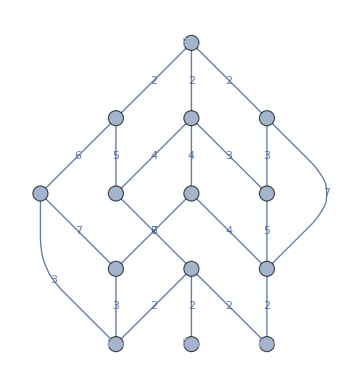
a) Graph, 𝒢=-Graphics-

```mathematica
(* Build data structure of graph - directed edges (going eastbound with weights *)
𝓋 ={Subscript[ES, #]&/@Range[4],Subscript[S, #]&/@Range[10]} //Flatten;
(* "hand-coded" set of directed edges with weights: 
DirectedEdge[from,to,weight] *)
eset = {{Subscript[ES, 1], 1,2},{Subscript[ES, 1], 2,2},{Subscript[ES, 1],3,2},{1,4,3},{1,8,7},{2,4,3},{2,5,4},{2,6,4},{3,6,5},{3,7,6},{4, 8,5},{5,8,4},{5,10,6},{6,9,7},{7,10,7},{7,Subscript[ES, 4],3},{8, Subscript[ES, 2],2},{9,Subscript[ES, 2],2},{9,Subscript[ES, 3],2},{9,Subscript[ES, 4],2},{10,Subscript[ES, 4],3}};
(* constructe the set of (directed) edges with weights *)
ℯ =DirectedEdge[Part[#,1],Part[#,2],Part[#,3]]&/@eset;
(* constructe the set of (directed) edges without weights *)
𝓀=ℯ[[#,1]]->ℯ[[#,2]]&/@Range[1,Length[ℯ]];
(* constructe the set of weights *)
𝓌=ℯ[[#,3]]&/@Range[1,Length[ℯ]];
(* constructe the set of edge labels *)
ℓ=( 𝓀[[#]]->𝓌[[#]])&/@ Range[1,Length[ℯ]];

(* Plot graph *)
𝒢=Graph[𝓀,
VertexLabels->Placed["Name",Center],
VertexSize->Medium,
EdgeShapeFunction->"FilledArcArrow",
EdgeLabels->ℓ,
EdgeWeight->𝓌];
Print["a) Graph, 𝒢=",Show[𝒢,ImageSize->Medium]];
```

a) Using Mathematica functions, we discover that there are six alternative routes in total between ES_1 and ES_2.

```mathematica
Subscript[pathsToES, 2]=FindPath[𝒢,Subscript[ES, 1],Subscript[ES, 2],∞, All];
Subscript[numPathsToES, 2] = Length[Subscript[pathsToES, 2]];
Print["ES_1 -> ES_2:"];
Do[Print["Path ",i,": ",Subscript[pathsToES, 2][[i]]],{i,Length[Subscript[pathsToES, 2]]}];
```

ES_1 -> ES_2:

Path 1: {ES_1,1,8,ES_2}

Path 2: {ES_1,3,6,9,ES_2}

Path 3: {ES_1,2,6,9,ES_2}

Path 4: {ES_1,2,5,8,ES_2}

Path 5: {ES_1,2,4,8,ES_2}

Path 6: {ES_1,1,4,8,ES_2}

b) Using Mathematica functions, we discover all paths from ES_1to ES_i:

```mathematica
Print["ES_1 -> ES_2:"];
Do[Print["Path ",i,": ",Subscript[pathsToES, 2][[i]]],{i,Length[Subscript[pathsToES, 2]]}];
Print["\n"];

Subscript[pathsToES, 3]=FindPath[𝒢,Subscript[ES, 1],Subscript[ES, 3],∞, All];
Subscript[numPathsToES, 3] = Length[Subscript[pathsToES, 3]];
Print["ES_1 -> ES_3:"];
Do[Print["Path ",i,": ",Subscript[pathsToES, 3][[i]]],{i,Length[Subscript[pathsToES, 3]]}];
Print["\n"];

Subscript[pathsToES, 4]=FindPath[𝒢,Subscript[ES, 1],Subscript[ES, 4],∞, All];
Subscript[numPathsToES, 4] = Length[Subscript[pathsToES, 2]];
Print["ES_1 -> ES_4:"];
Do[Print["Path ",i,": ",Subscript[pathsToES, 4][[i]]],{i,Length[Subscript[pathsToES, 4]]}];
```

ES_1 -> ES_2:

Path 1: {ES_1,1,8,ES_2}

Path 2: {ES_1,3,6,9,ES_2}

Path 3: {ES_1,2,6,9,ES_2}

Path 4: {ES_1,2,5,8,ES_2}

Path 5: {ES_1,2,4,8,ES_2}

Path 6: {ES_1,1,4,8,ES_2}

ES_1 -> ES_3:

Path 1: {ES_1,3,6,9,ES_3}

Path 2: {ES_1,2,6,9,ES_3}

"

ES_1 -> ES_4:

Path 1: {ES_1,3,7,ES_4}

Path 2: {ES_1,3,7,10,ES_4}

Path 3: {ES_1,3,6,9,ES_4}

Path 4: {ES_1,2,6,9,ES_4}

Path 5: {ES_1,2,5,10,ES_4}

In total we have 13 different paths between ES_1to ES_i.

c) Using Mathematica functions, we find the shortest path from ES_1to ES_i:

```mathematica
shortestPaths= {};
Do[
shortestPath = FindShortestPath[𝒢,Subscript[ES, 1],Subscript[ES, i]];
Print["Shortest path ES_1 -> ", Subscript[ES, i],": ", shortestPath]
AppendTo[shortestPaths, shortestPath];
, {i, 2, 4}
];
```

Shortest path ES_1 -> ES_2: {ES_1,1,8,ES_2}

Shortest path ES_1 -> ES_3: {ES_1,2,6,9,ES_3}

Shortest path ES_1 -> ES_4: {ES_1,3,7,ES_4}

d) Using Mathematica functions, we find the cost of the shortest path from ES_1to ES_i:

```mathematica
Do[
Print["Shortest path cost ES_1 -> ", Subscript[ES, i],": ", GraphDistance[𝒢,Subscript[ES, 1],Subscript[ES, i]]];
, {i, 2, 4}
];
```

Shortest path cost ES_1 -> ES_2: 11.

Shortest path cost ES_1 -> ES_3: 15.

Shortest path cost ES_1 -> ES_4: 11.

e) Using Mathematica function, the shortest paths in the graph is highlighted. We can see that the combination of the shortest paths does not cover all of the stops in the system. This means that if the buses were to only use those routes, there are some stops and passengers that never would get served - which probably isn’t the best way to go.

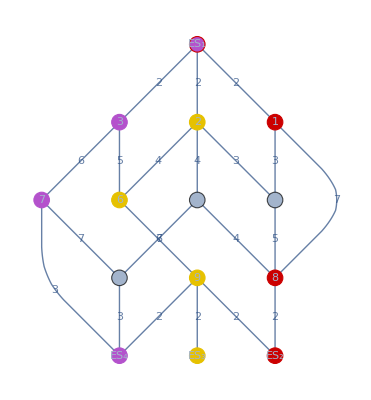

```mathematica
HighlightGraph[𝒢, shortestPaths]
```

#### Useful functions for IV.C.2

```mathematica
(* Summarise the average number in the system along the "path" - assuming an M/M/1 queue at each bus stop *)
𝒩[path_:List]:=Module[{},
Plus@@Flatten[{QueueProperties[QueueingProcess[Subscript[λ, #],M],"MeanSystemSize"] &/@ path}]
] 

(* Returns the route with the highest number of waiting passengers *)
ℳ[path_]:=Module[{Ntmp,wh,pos},
(* Determine the total number of passengers along each of the routes *) 
Ntmp= 𝒩[#]&/@ path /. Λ;
(* Select the route with the highest number of passengers *)
wh=Select[Ntmp,#>=Max[Ntmp]&];
pos=Position[Ntmp,wh[[1]]][[1]];
(* Return the selected path and the corresponding number of passengers *)
{path[[pos[[1]]]], 𝒩[path[[pos[[1]]]]]/. Λ}
]

(* Returns a random route with the number of waiting passengers *)
ℳR[path_]:=Module[{wh,pos},
(* Select the route randomly among the alternatives in path *)
pos=RandomInteger[{1,Length[path]}];
(* Return the selected path and the corresponding number of passengers *)
{path[[pos]], 𝒩[path[[pos]]]/. Λ}
]
```

#### IV.C.2*

After a DDOS attack on the on the bus company’s server you don’t know the state (number/waiting time of passengers) at each station. The busses can still run, but you have to select the next route randomly. In this task, you are going to determine the consequence of that you must select the route randomly and not optimally.  

First, we need a metric to quantify how good a route is.  Let’s assume that this is the sum of passengers at each station along the route (which can be served by this bus).  Each bus stop is an M/M/1 queue with the arrival rate defined in the set Λ below.  The service rate at each bus stop is M=3.   Above you find three functions (𝒩[ ], ℳ[ ], ℳR[ ]) that can be helpful in obtaining the number of passengers waiting at each bus stop, and to summarize the total number along a predefined (the one with most passengers) and along a random route.

a) Find the routes between ES_1to ES_i(i=2,3,4) with the highest total number of passengers waiting. [you may use the function ℳ[ ] from above]
b) Now, assume that the bus coordination system is attacked and out of service.  Sample 1000 bus trips. [you may use the function ℳR[ ] from above].
c) Obtain the relative difference in number of passengers handled by informed and by random selection of routes, for each of the three pair of end stations: ES_1to ES_i(i=2,3,4).  Plot the relative difference, with the average and uncertainty of the estimator (choose your uncertainty metric, check the textbook for alternatives).

```mathematica
(* Parameters*)
M=0.3;
Λ={Subscript[λ, 1]->0.114,Subscript[λ, 2]->0.176,Subscript[λ, 3]->0.154,Subscript[λ, 4]->0.120,Subscript[λ, 5]->0.181,Subscript[λ, 6]->0.175,Subscript[λ, 7]->0.238,Subscript[λ, 8]->0.247,Subscript[λ, 9]->0.123,Subscript[λ, 10]->0.123};
```

a) The routes between ES_1to ES_i with the highest total number of passengers waiting are printed below.

```mathematica
Subscript[stopsToES, 2]= {};
Subscript[stopsToES, 3] = {};
Subscript[stopsToES, 4] = {};

Do[
	Do[
		path = Subscript[pathsToES, i][[j]];
		path = Drop[path, 1];
		path = Drop[path, -1];
		AppendTo[Subscript[stopsToES, i], path],
	{j, 1, Length[Subscript[pathsToES, i]]}
	],
{i, 2, 4}
];

Do[
	Print["Route from ES_1 -> " Subscript[ES, i], " with the highest number of passengers: ", ℳ[Subscript[stopsToES, i]]],
	{i, 2, 4} 
];
```

Route from ES_1 ->  ES_2 with the highest number of passengers: {{2,5,8},7.60074}

Route from ES_1 ->  ES_3 with the highest number of passengers: {{2,6,9},3.51427}

Route from ES_1 ->  ES_4 with the highest number of passengers: {{3,7,10},5.58842}

b) Sampling is done in cell below. Chose to only print the first five samples for practical reasons.

```mathematica
Subscript[resultES, 2]={};
Subscript[resultES, 3]={};
Subscript[resultES, 4]={};

Do[
result=Reap[
Do[
route=ℳR[Subscript[stopsToES, j]];
Sow[route],
{i,1,1000}
]
][[2,1]];
Switch[j,2,Subscript[resultES, 2]=result,3,Subscript[resultES, 3]=result,4,Subscript[resultES, 4]=result],
{j,2,4} 
];

Print["First five samples ES_1 -> ES_2: \n",Subscript[resultES, 2][[1 ;;5]]]
```

First five samples ES_1 -> ES_2: 
{{{3,6,9},3.14971},{{2,5,8},7.60074},{{3,6,9},3.14971},{{2,6,9},3.51427},{{2,5,8},7.60074}}

c) The relative difference is visualised in the bar plot below. I chose to use standard error to  show the uncertainty in our measurements. The standard error gives an idea of how much the average relative difference might vary due to sampling. This helps us understand how reliable our estimate is by showing both the average difference and the likely range around it, giving more confidence in the results shown in the plot.

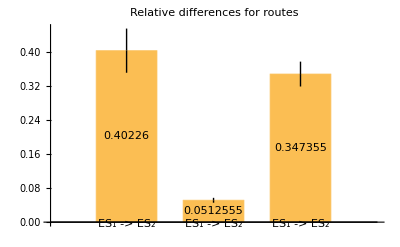

```mathematica
informed = {7.60074, 3.51427, 5.58842};

average= {};
Do[
 avg = Mean[Subscript[resultES, i][[All,2]]];
AppendTo[average, avg],
{i , 2, 4}
]

relativeDiffs = {};
Do[
 diff = (informed[[i]]- average[[i]])/ average[[i]];
AppendTo[relativeDiffs, diff],
{i , 1, 3}
]

stdErrors = {};
Do[
 std = StandardDeviation[Subscript[resultES, i][[All,2]]];
stdErr = std / Sqrt[Length[Subscript[resultES, i]]];
AppendTo[stdErrors, stdErr],
{i , 2, 4}
]

labels = {"ES_1 -> ES_2", "ES_1 -> ES_3", "ES_1 -> ES_4"};

plotMaterial = {};
Do[
Subscript[numbES, i]= {Around[relativeDiffs[[i]], stdErrors[[i]]]};
AppendTo[plotMaterial, Subscript[numbES, i]],
{i, Length[relativeDiffs]}
]

BarChart[
plotMaterial,
ChartLabels->labels,
PlotLabel->"Relative differences for routes",
LabelingFunction->(Placed[#,Center]&)
]
```

The labels in the plot are wrong as something got locked up, but the correct labeling would be "ES_1 -> ES_2", "ES_1 -> ES_3", "ES_1 -> ES_4".


d) The bar plot shows that the relative difference in passengers handled is much higher for the first and third routes (ES_1 -> ES_2 and ES_1 -> ES_4) than for the second (ES_1 -> ES_3). This indicates that the bus coordination system significantly improves passenger handling on certain routes, especially those with higher or more variable demand. Overall, the coordination system is essential for efficiently managing waiting passengers, particularly on busier routes.

### Task IV.D - Reflections

a) Have you used any AI tool? How and for what have you used it, and how useful did you find it?
b) What have you learned from this assignment?  Challenges you have been facing, usability of the tool, relevance for you own interest and studies, etc.

a) I have used ChatGPT to help me with some clever Mathematica hacks. Even though standard googling and searching Mathematica docs turned out to be more efficient most of the time, ChatGPT were able to help me a handful of times. 

b) I have learned a lot of Mathematica from this lab. I don’t feel like I have been facing a lot of challenges during this lab to be honest. The biggest problem was understanding some of the tasks where I found the phrasing somewhat unclear. After this lab I am a much bigger fan of Mathematica as a tool, and I have learned that it is a very powerful (and cool) tool. As I have said in the previous labs, really like this assignment and have found it surprisingly educational.